```mathematica
trikotnik = Trikotnik[{0,0},{5,1},{7,4}]
```

Trikotnik[{0,0},{5,1},{7,4}]

```mathematica
Stranice[Trikotnik[A_,B_,C_]]:={
Daljica[A,B],Daljica[B,C],Daljica[A,C]
}
```

```mathematica
Stranice[trikotnik]
```

{Daljica[{0,0},{5,1}],Daljica[{5,1},{7,4}],Daljica[{0,0},{7,4}]}

```mathematica
Koti[Trikotnik[A_,B_,C_]] :={
Kot[C,A,B],Kot[A,B,C],Kot[B,C,A]
}
```

```mathematica
Koti[trikotnik]/Degree //N
```

{18.4349,135.,26.5651}

```mathematica
Kot[A_,B_,C_] :=ArcCos[((A-B).(C - B))/(Norm[A-B]*Norm[C - B])]
```

```mathematica
Graphics[{Point[{0,0}],Point[{5,1}],Point[{7,4}]}]
```

-Graphics-

```mathematica
SlikaOgljisc[Trikotnik[A_,B_,C_]] :={
Point[A],Point[B],Point[C]
}
```

```mathematica
Graphics[SlikaOgljisc[trikotnik]]
```

-Graphics-

```mathematica
SlikaStranic[Trikotnik[A_,B_,C_]] :={
Line[{A,B}],Line[{B,C}],Line[{C,A}]
}
```

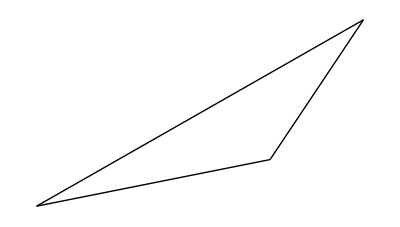

```mathematica
Graphics[SlikaStranic[trikotnik]]
```

```mathematica
NarisiTrikotnik[trikotnik_] :=Graphics[{SlikaOgljisc[trikotnik],SlikaStranic[trikotnik]}]
```

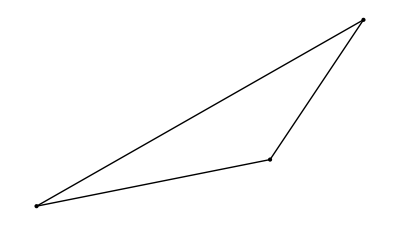

```mathematica
NarisiTrikotnik[trikotnik]
```